```mathematica
Quit
```

Host and port:

```mathematica
host="18.217.160.48";
port="80";
```

Local process id:

```mathematica
$ProcessID
```

17160

#### GET

With GET:

```mathematica
EvaluationRequest[<|"Host"->host,"Port"->port,"Method"->"GET"|>,{$ProcessID,$MachineName}]
```

{2929, ip-172-31-39-91}

#### POST

With POST and BASE64:

```mathematica
EvaluationRequest[<|"Host"->host,"Port"->port,"Method"->"POST","Encoding"->"Base64"|>,{$ProcessID,$MachineName}]
```

Base64

{2929, ip-172-31-39-91}

With POST and ByteArray (Wolfram Language only):

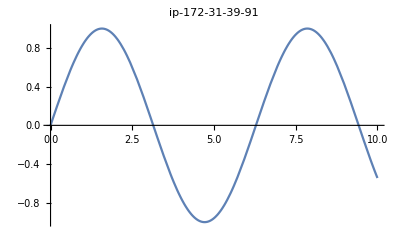

```mathematica
EvaluationRequest[<|"Host"->host,"Port"->port,"Method"->"POST","Encoding"->"ByteArray"|>,Plot[Sin[x],{x,0,10},PlotLabel->$MachineName]]
```